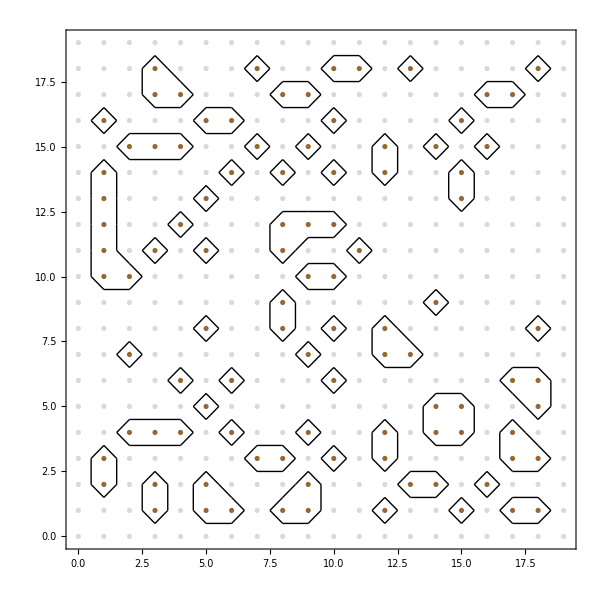

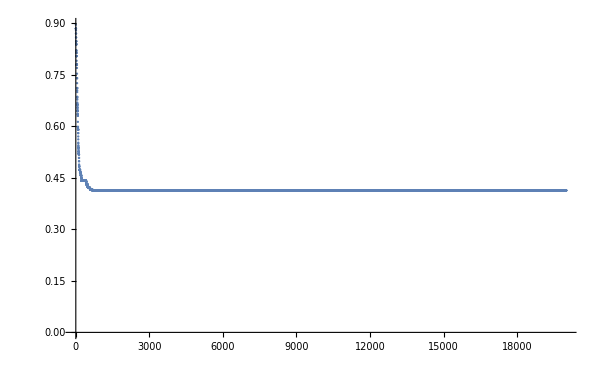

```mathematica
infoData=Import[NotebookDirectory[]<>"out/x64-Release/output-info.txt","Table"];

data=Import[NotebookDirectory[]<>"out/x64-Release/output-boundary.txt","Table"];
data=Partition[#,2]&/@data;

rawdata=Import[NotebookDirectory[]<>"out/x64-Release/output-raw.txt","Table"];
disks=MapIndexed[{If[#1==1,Brown,LightGray],Disk[#2-{1,1},0.1]}&,Transpose@rawdata,{2}];

Graphics[{disks,Line[data]},ImageSize->600,Frame->True]

ListPlot[infoData,PlotRange->All]
```

```mathematica
BinaryReadList[NotebookDirectory[]<>"out/x64-Release/test.bin", "UnsignedInteger64",1]
```

{234}

```mathematica
Join[Table["Real64",9],Table["Integer32",2]]
```

{Real64,Real64,Real64,Real64,Real64,Real64,Real64,Real64,Real64,Integer32,Integer32}

```mathematica
file = OpenRead[filename, BinaryFormat->True];
d=First@BinaryReadList[file, "Integer32",1];
```

```mathematica
(*Indices are: x,y, velX,velY, dens, press, intEnergy, kinEnergy, Dummy, group, id*)
LoadCube[filename_]:=Module[{d,dims,dataAndHeaders},
file = OpenRead[filename, BinaryFormat->True];
d=First@BinaryReadList[file, "UnsignedInteger64",1];
dims=BinaryReadList[file, "UnsignedInteger64",d];
Print["Dimensions: ",dims];
dataAndHeaders=TakeDrop[BinaryReadList[file, "Real64"],Times@@dims];
Close[file];
{ArrayReshape[dataAndHeaders[[1]],dims],TakeList[dataAndHeaders[[2]],dims]}]
```

```mathematica
{partics, headers}=LoadCube[NotebookDirectory[]<>"out/x64-Release/glass2d.binary"];
groupCols={RGBColor[0.49, 0.63, 0.96],Black};
Manipulate[Graphics[{groupCols[[#[[10]]+1]],Disk[#[[{1,2}]],0.005]}&/@partics[[i]], PlotRange->{{0,1},{0,1}},Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1}]
```

Dimensions: {1001,405,11}

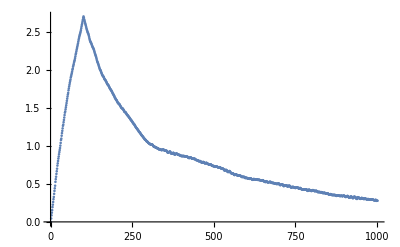

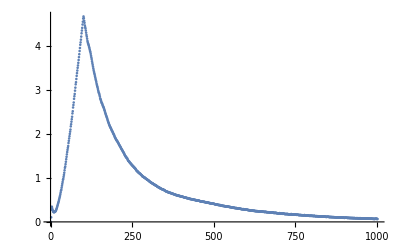

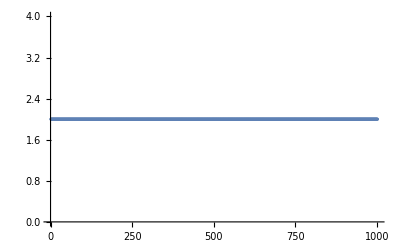

```mathematica
ListPlot[Total[partics[[All,All,3]],{2}]/Dimensions[partics][[2]]]
ListPlot[Total[partics[[All,All,8]],{2}]]
ListPlot[Total[partics[[All,All,7]],{2}]]
```

```mathematica
Manipulate[ListDensityPlot[{#[[1]],#[[2]],#[[5]]}&/@partics[[i]], PlotRange->{{0,1},{0,1},All},
Mesh->All,InterpolationOrder->0,ColorFunction->ColorData[{"Rainbow",{0.5,1.2}}],ColorFunctionScaling->False,ClippingStyle->Automatic,
PlotLegends->Automatic,Frame->True,AspectRatio->1,ImageSize->600],{i,1,Length@partics,1}]
```